## Basic Evolution

Basic evolution:

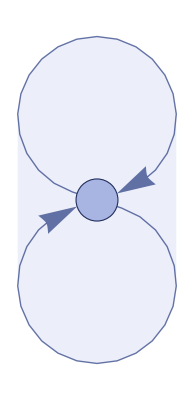
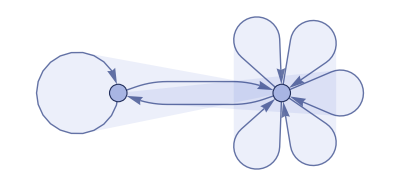
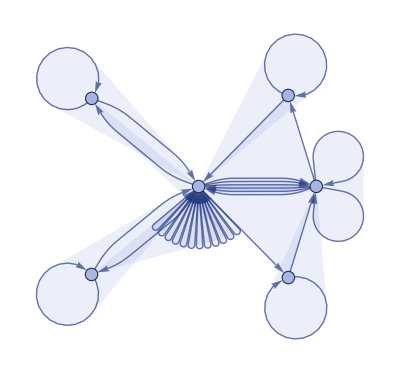
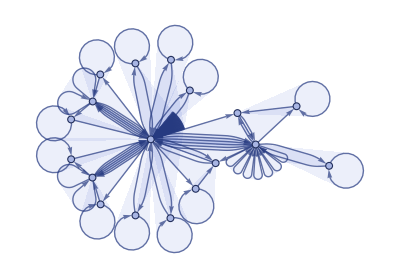
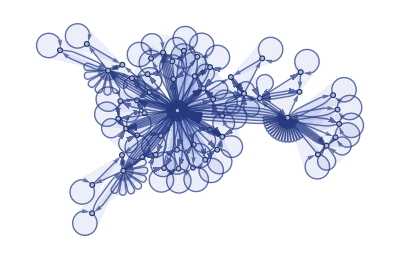

```mathematica
[{{{1,1,2}}->{{2,2,2},{2,1,2},{1,2,3},{3,3,1}}},{{1,1,1}},4,"StatesPlotsList"]
```

Event-by-event evolution:

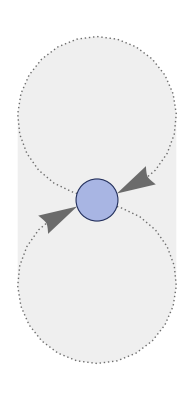
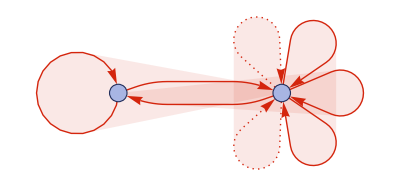
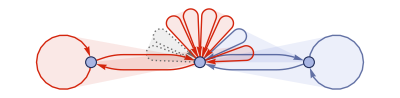
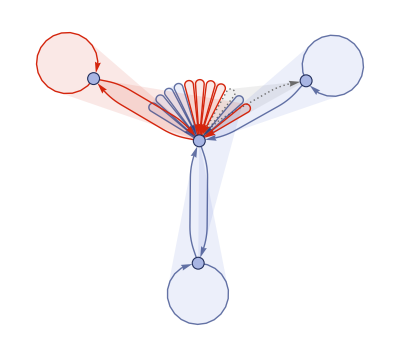
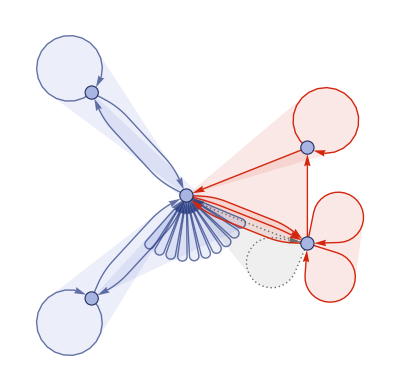
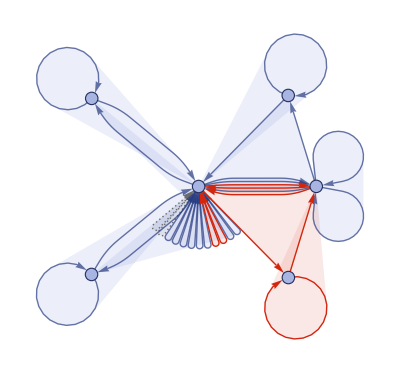
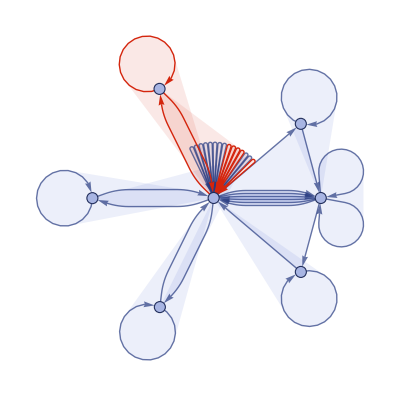

```mathematica
[{{{1,1,2}}->{{2,2,2},{2,1,2},{1,2,3},{3,3,1}}},{{1,1,1}},<|"MaxEvents"->6|>,"EventsStatesPlotsList"]
```

Vertex and edge counts:

```mathematica
{vertexCountList,edgeCountList}=[{{{1,1,2}}->{{2,2,2},{2,1,2},{1,2,3},{3,3,1}}},{{1,1,1}},9,{"VertexCountList","EdgeCountList"}];
```

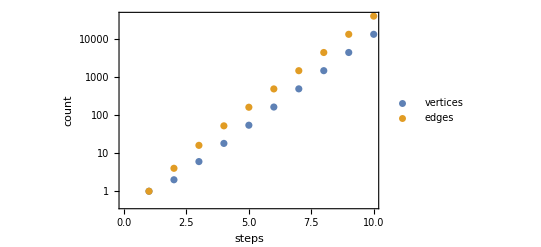

```mathematica
ListLogPlot[{vertexCountList,edgeCountList},]
```

Symbolic expression for vertex count:

```mathematica
FindSequenceFunction[vertexCountList,t]
```

DifferenceRoot[Function[{y,n},{-3 y[n]+y[1+n]==0,y[1]==1,y[2]==2}]][t]

Symbolic expression for edge count:

```mathematica
FindSequenceFunction[edgeCountList,t]
```

DifferenceRoot[Function[{y,n},{-4-3 y[n]+y[1+n]==0,y[1]==1,y[2]==4}]][t]

Result after 4 generations:

```mathematica
["FinalStatePlot"]
```

-Graphics-

## Causal Graph

Causal graph:

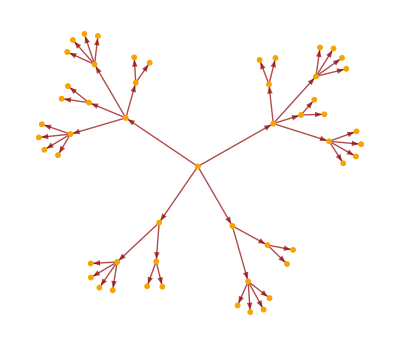

```mathematica
["CausalGraph",]
```

Layered rendering:

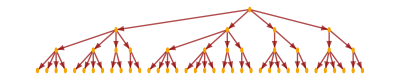

```mathematica
["LayeredCausalGraph"]
```

Causal graph distance matrix:

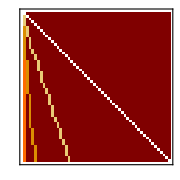

```mathematica
MatrixPlot[Transpose[GraphDistanceMatrix[["CausalGraph"]]],]
```

## Final State Properties

Hypergraph adjacency matrix:

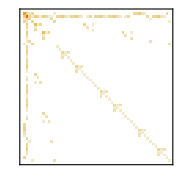

```mathematica
MatrixPlot[AdjacencyMatrix@Catenate[Map[UndirectedEdge@@@Subsets[#,{2}]&,["FinalState"]]],]
```

Vertex degree distribution:

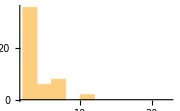

```mathematica
Histogram[Values[Counts[Catenate[Union/@["FinalState"]]]],]
```

Neighborhood volumes (ignoring directedness of connections):

```mathematica
volumes=[Values[[["FinalState"],All,Automatic]]];
```

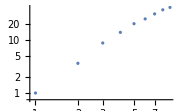

```mathematica
ListLogLogPlot[volumes,]
```

Effective dimension versus radius:

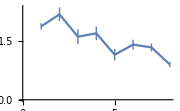

```mathematica
ListLinePlot[[volumes],]
```

Successive neighborhood balls around a random vertex:

```mathematica
[["FinalState"],4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Distance matrix:

```mathematica
distanceMatrix=GraphDistanceMatrix[UndirectedGraph[[["FinalState"]]]];
```

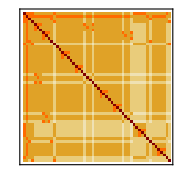

```mathematica
MatrixPlot[Exp[-(distanceMatrix/. 0->None)],]
```

Distribution of distances in the graph:

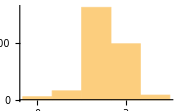

```mathematica
Histogram[Flatten[distanceMatrix],]
```

## Spreading of Effects

Causal graph adjacency matrix:

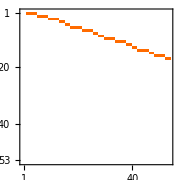

```mathematica
MatrixPlot[AdjacencyMatrix[["CausalGraph"]],]
```

Neighborhood volumes in causal graph:

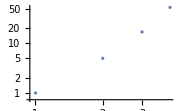

```mathematica
ListLogLogPlot[Values[[["CausalGraph"],{1}]],]
```

## Other Evolution Orders

Random evolutions:

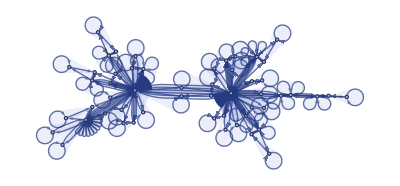

```mathematica
[{{{1,1,2}}->{{2,2,2},{2,1,2},{1,2,3},{3,3,1}}},{{1,1,1}},<|"MaxEvents"->53|>,"FinalStatePlot","EventOrderingFunction"->"Random"]
```

Different deterministic evolution orders:

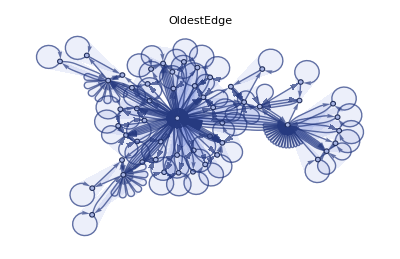
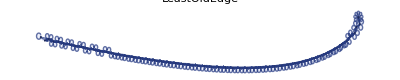
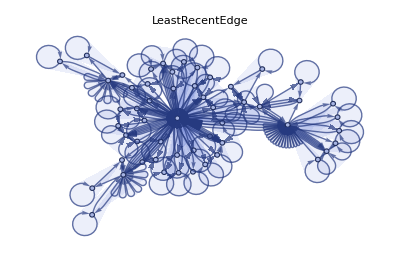
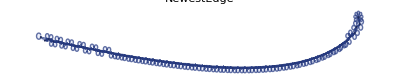
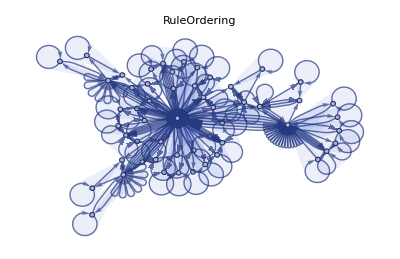
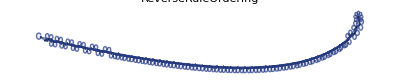

```mathematica
[{{{1,1,2}}->{{2,2,2},{2,1,2},{1,2,3},{3,3,1}}},{{1,1,1}},<|"MaxEvents"->53|>,"EventOrderingFunction"->{#,"LeastRecentEdge","RuleOrdering","RuleIndex"}]["FinalStatePlot",PlotLabel->#]&/@{"OldestEdge","LeastOldEdge","LeastRecentEdge","NewestEdge","RuleOrdering","ReverseRuleOrdering"}
```

## Graph Features of States

```mathematica
graph=[["FinalState"]];
```

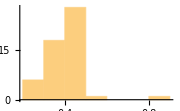

```mathematica
Histogram[ClosenessCentrality[graph],]
```

Cycle properties:

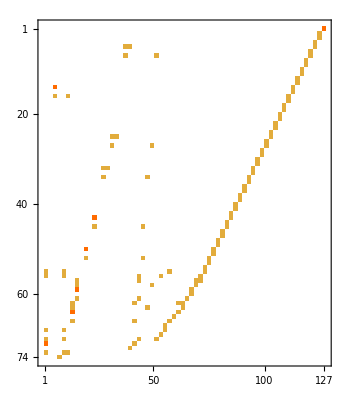

```mathematica
EdgeCycleMatrix[UndirectedGraph[graph]]//MatrixPlot
```

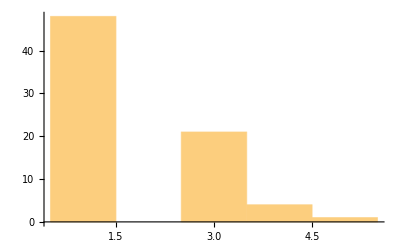

```mathematica
Histogram[Length/@FindFundamentalCycles[UndirectedGraph[graph]]]
```

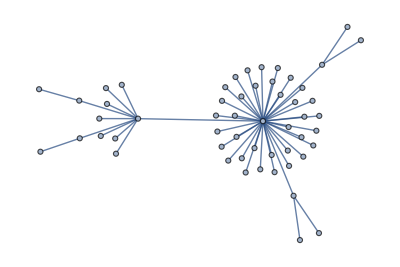

```mathematica
FindSpanningTree[UndirectedGraph[graph]]
```